## Question 1

### a)

```mathematica
X1 = NormalDistribution[3,2]
```

NormalDistribution[3,2]

```mathematica
MomentGeneratingFunction[X1,t]
```

ⅇ^(3 t+2 t^2)

```mathematica
X2=NormalDistribution[3,2]
```

NormalDistribution[3,2]

```mathematica
MomentGeneratingFunction[X2,t]
```

ⅇ^(3 t+2 t^2)

### b)

```mathematica
Y=TransformedDistribution[ 5A-2B+6, {A\[Distributed]X1,B\[Distributed]X2}]
```

NormalDistribution[15,2 √29]

```mathematica
MomentGeneratingFunction[Y,t]
```

ⅇ^(15 t+58 t^2)

```mathematica
Plot[Evaluate[MomentGeneratingFunction[Y,t]], {t,0,2}]
```

-Graphics-

## Question 2

```mathematica
Plot[12*Evaluate[PDF[UniformSumDistribution[12],x] /. {x -> y*12}], {y,0,1}]
```

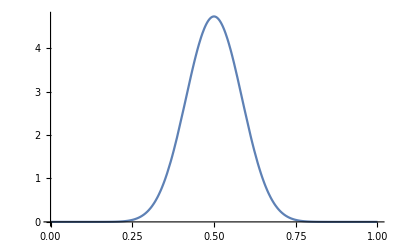

```mathematica
t1 = TransformedDistribution[U^(1/3),U \[Distributed] UniformDistribution[]]
```

BetaDistribution[3,1]

```mathematica
tf=TransformedDistribution[A+B,{A\[Distributed]t1,B\[Distributed]t1}]
```

TransformedDistribution[x1+x2,{x1\[Distributed]BetaDistribution[3,1],x2\[Distributed]BetaDistribution[3,1]}]

```mathematica
ee= PDF[tf]
```

Function[x,Piecewise[{{(3 x^5)/10, 0<x≤1}, {18/5-9 x+6 x^2-(3 x^5)/10, 1<x<2}, {0, True}}],Listable]

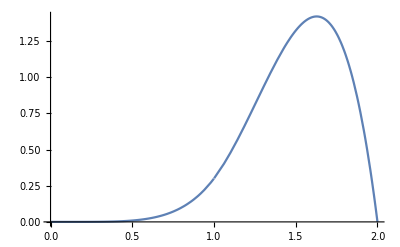

```mathematica
Plot[ee[x],{x,0,2}]
```